```mathematica
eRad= 2.81794*^-5; (*classical electron radius in Angstroms*)
polFactor=5000.0;(*polarization factor (set to 1 for now),can basically be constant might be function of theta*)
layersInSample=5;(*total number of crystal layers (i.e.materials in heterostructure)*)
wavelength = 0.709; (*x-ray wavelength from molybdenum K-alpha1*)
scaling =(* None*) "Log";
imageDimensions = {1000,1000};

(*d-spacing (Angstroms) of crystal layers from (001) direction*)
(*data taken from ICSD database:https://icsd.fiz-karlsruhe.de/search/index.xhtml*)(*Specific Sources can be found with the Collection Codes*)
(*length of cell in c-direction in database is what was taken as d-spacing*)
dSrTiO3=3.905;(*Code:23076*)
dSrRuO3 =3.964;(*Code:82977*)(*was 5.569*)
dBiFeO3 =4.072;(*Code:15299*)(*was 13.867 according to ICSD*)
dCobalt = 4.089;(*Code:44990*)
dPlatinum = 3.924;(*Code:5250*)
dSpace={dSrTiO3, dSrRuO3, dBiFeO3, dCobalt, dPlatinum};(*list of d-spacings of each crystal layer in sample*)

(*average number density of layer (atoms/cubic Angstrom)*)
(*acquired using data from ICSD*)
densSrTiO3=8.396*^-2;(*was 8.396*^-2 atoms/cubic Angstrom*)
densSrRuO3=8.2706*^-2;(*was 8.2706*^-2*)
densBiFeO3=8.8864*^-2;
densCobalt=8.9969*^-2;
densPlatinum=6.6214*^-2;
rho={densSrTiO3, densSrRuO3, densBiFeO3, densCobalt, densPlatinum};

(*list of average number densities of each layer in sample*)(*experiment uses x-rays from molybdenum K-alpha1 (wavelength~0.709 Ang,energy~17.4793 keV) http://www.med.harvard.edu/jpnm/physics/refs/xrayemis.html*)(*data taken from online NIST form factor tables http://physics.nist.gov/PhysRefData/FFast/html/form.html*)(*notable discrepancy is that data from NIST was taken for waves of energy~17.59961 keV*)(*only the real part of the atomic form factor is considered*)
affSr=36.899;(*atomic form factor of strontium e/atom*)
affTi=22.3139;
affO=8.01434;
affRu=42.9479;
affBi=80.0284;
affFe=26.4094;
affCo=27.4188;
affPt=77.1783;
affSrTiO3=affSr+affTi+3*affO;
affSrRuO3=affSr+affRu+3*affO;
affBiFeO3=affBi+affFe+3*affO;
formFactor={affSrTiO3, affSrRuO3, affBiFeO3, affCo, affPt};(*list of form factors for each layer in sample*)

(*Manipulable variable defaults*)
nBarDefaults = {500, 54.014, 142.645, 23.97, 68.04};
nMin = 1;
nMax = 600;
nStep = 0.1;

mDefaults = {500, 56, 157, 24, 69};
mMin = 1;
mMax = 600;
mStep = 1;

delDefaults = {0.2264, 2.292,4.09, 1.0};
delMin = 0.001;
delMax = 10.0;
delStep = 0.1;

qInitDefault=1.4;
qFinDefault=1.8;

pointsPlotted = 200;
plotPointRecursion = 0;


(*******************************************************************************************************************)


(*functions for calculating specular reflectivity as outlined by Paul Miceli in Semiconductor Interfaces,Microstructures,and Devices:Properties and Applications p.87:X-ray Reflectivity from Heteroepitaxial Layers*)(*independent variable is qZ,the vertical component of the scattering vector Q.all other parameters are constants defined above or to be manipulated in simulation*)rSpec[qZ0_,polFactor0_,eRad0_,layerNum0_,rho0_,dSpace0_,formFactor0_,mL0_,nBar0_,deltaL0_]:=Module[{qZ=qZ0,polFactor=polFactor0,eRad=eRad0,layerNum=layerNum0,rho=rho0,dSpace=dSpace0,formFactor=formFactor0,mL=mL0,nBar=nBar0,deltaL=deltaL0,r},

r=Abs[polFactor*(16*Pi^2*eRad^2/qZ^2)*Norm[scatAmp[qZ,layerNum,rho,dSpace,formFactor,mL,nBar,deltaL]]^2];
(*Echo[N[r]];*)
(*Echo[N[Norm[scatAmp[qZ,layerNum,rho,dSpace,formFactor,mL,nBar,deltaL]]]];*)
r
]



(*the average scattering amplitude*)
scatAmp[qZ0_,layerNum0_,rho0_,dSpace0_,formFactor0_,mL0_,nBar0_,deltaL0_]:=
Module[{qZ=qZ0,layerNum=layerNum0,rho=rho0,dSpace=dSpace0,formFactor=formFactor0,mL=mL0,nBar=nBar0,deltaL=deltaL0,vL,i,aSub,aL,sum},
(*Echo[qZ];*)
vL=Table[calcV[qZ,j,dSpace[[j]],mL[[j]],nBar[[j]]],{j,layerNum}];
i=1;
aSub=rho[[i]]*dSpace[[i]]*formFactor[[i]]*vL[[i]]/(1-Exp[-I*qZ*dSpace[[i]]]);
sum=aSub;

i=2;
While[i<=layerNum,
aL=rho[[i]]*dSpace[[i]]*formFactor[[i]]*(vL[[i]]-1)/(1-Exp[-I*qZ*dSpace[[i]]]);
sum+=Product[vL[[j]],{j,i-1}]*Exp[I*qZ*Sum[deltaL[[j]],{j,i-1}]]*aL;
i++;
(*Echo[i];*)
];
(*Echo[sum];*)

sum
]



(*calculate V,essentially the roughness*)
calcV[qZ0_,i0_,d0_,m0_,n0_]:=
Module[{qZ=qZ0, i=i0, d=d0, m=m0, n=n0},
	If[i==1,
	Exp[-2*n*(1-(n/m))*Sin[0.5*qZ*d]^2],

	((n/m)*Exp[I*qZ*d]+(1-(n/m)))^m
]
]

(*getResiduals[]*)



thetaToQ[twoTheta_]:=(4*Pi*Sin[twoTheta/2  Degree] / wavelength)


(*******************************************************************************************************************)


(*Set up plots of BFO Reflectivity data taken by Jesse Kremenak*)

Needs["ErrorBarPlots`"]; (*load up Error Bar Plots package*)
(*  b986-1-Bragg001-2theta  *)
data986Bragg001Theta = Import["Z:\\xrd_mathematica\\BFO_Reflectivity_data\\b986-1-Bragg001-final.dat", "Table"] ;(*import data from file*)
For[i=1,i≤Length[data986Bragg001Theta],i++,
	data986Bragg001Theta[[i,1]]=thetaToQ[data986Bragg001Theta[[i,1]]];
];
plotReadyData = Table[{data986Bragg001Theta[[i,{1,2}]], ErrorBarPlots`ErrorBar[data986Bragg001Theta[[i,3]]]}, {i,Length[data986Bragg001Theta]}];
plot986Bragg001Theta = ErrorListPlot[plotReadyData, ScalingFunctions->scaling, ImageSize->imageDimensions, PlotLegends->{"b986 (001) Q"}];

(*  b987-1-Bragg001-2theta  *)
data987Bragg001Theta = Import["Z:\\xrd_mathematica\\BFO_Reflectivity_data\\b987-1-Bragg001-final.dat", "Table"] ;(*import data from file*)
For[i=1,i≤Length[data987Bragg001Theta],i++,
	data987Bragg001Theta[[i,1]]=thetaToQ[data987Bragg001Theta[[i,1]]];
];
plotReadyData2 = Table[{data987Bragg001Theta[[i,{1,2}]], ErrorBarPlots`ErrorBar[data987Bragg001Theta[[i,3]]]}, {i,Length[data987Bragg001Theta]}];
plot987Bragg001Theta = ErrorListPlot[plotReadyData2, ScalingFunctions->scaling, ImageSize->imageDimensions,PlotStyle->Red, PlotLegends->{"b987 (001) θ"}];

(*  b987-1-Bragg001-q  *)
data987Bragg001Q = Import["Z:\\xrd_mathematica\\BFO_Reflectivity_data\\b987-1-Bragg001-final-q.txt", "Table"] ;(*import data from file*)
plotReadyData3 = Table[{data987Bragg001Q[[i,{1,2}]], ErrorBarPlots`ErrorBar[data987Bragg001Q[[i,3]]]}, {i,Length[data987Bragg001Q]}];
plot987Bragg001Q = ErrorListPlot[plotReadyData, ScalingFunctions->scaling, ImageSize->imageDimensions, PlotLegends->{"b987 (001) Q"}];

fitData=Drop[data987Bragg001Theta, None, {3}];
(*******************************************************************************************************************)
(*
(* Perform nonlinear least squares fitting on model to get desired parameter values *)

(* First, set up parameters to be fitted *)
fitParams ={{ delSrTiO3,delDefaults[[1]]},{ delSrRuO3,delDefaults[[2]]},{ delBiFeO3,delDefaults[[3]]}};

(* Prepare data *)
fitData=Drop[plotReadyData2, None, {2}];
nBar={nSrTiO3,nSrRuO3,nBiFeO3,nCo,nPt};
deltaL={delSrTiO3,delSrRuO3,delBiFeO3,delCo};
layerNum=4;
qRange1={q,qInitDefault,qFinDefault};

nlm=NonlinearModelFit[fitData, rSpec[q,polFactor,eRad,layerNum,rho,dSpace,formFactor,mL,nBar,deltaL], fitParams, q]
Plot[nlm[q],qRange1,Epilog:>Point[fitData],PlotStyle->{Orange,Thick}]

*)

(*******************************************************************************************************************)

(*Now with constants and functions declared,let's run our model*)
(*We use the function Manipulate to vary the parameters we want (namely nBar,mL,and deltaL) so that we can see changes to our plotted fit in real time.To use Manipulate in this way,we call our function to be graphed inside of a plotting function.Then we provide manipulate with each of the variables we wish to tweak during the simulation and with a possible range of manipulation*)
(*let's see how fast it is...*)

Manipulate[mL={mSrTiO3,mSrRuO3,mBiFeO3,mCo,mPt};
nBar={nSrTiO3,nSrRuO3,nBiFeO3,nCo,nPt};
deltaL={delSrTiO3,delSrRuO3,delBiFeO3,delCo};
deltaLFit={delSrTiO3Fit,delSrRuO3Fit,delBiFeO3Fit,delCoFit};
(*Echo[polFactor];*)
(*Echo[rSpec[2.0,polFactor,eRad,layerNum,rho,dSpace,formFactor,mL,nBar,deltaL]]*)
qRange={q,qInit,qFin};

(*
plotHandFit = Plot[rSpec[q,polFactor,eRad,layerNum,rho,dSpace,formFactor,mL,nBar,deltaL],qRange,PlotPoints->pointsPlotted,MaxRecursion->plotPointRecursion,
		ScalingFunctions->scaling,Frame->True,FrameLabel->{Style["Q (Å^-1)",16,Bold],Style["Reflectivity (counts/sec)",16,Bold]},ImageSize->imageDimensions, PlotLegends->{"fit"}];
*)

fitParams ={{ delSrTiO3Fit,delSrTiO3},{ delSrRuO3Fit,delSrRuO3},{delBiFeO3Fit, delBiFeO3}, {delCoFit,delCo}};
nlm=NonlinearModelFit[fitData, rSpec[q,polFactor,eRad,layerNum,rho,dSpace,formFactor,mL,nBar,deltaLFit], fitParams, q,MaxIterations->10000,Method->"Gradient"];
plotNonlinFit = Plot[nlm[q],{q,qInit,qFin},Epilog:>Point[fitData],PlotStyle->{Orange,Thick},
					ScalingFunctions->"Log",Frame->True,FrameLabel->{Style["Q (Å^-1)",16,Bold],Style["Reflectivity (counts/sec)",16,Bold]},ImageSize->imageDimensions, PlotLegends->{"fit"}];

Show[plotNonlinFit, (*plot986Bragg001Theta*)plot987Bragg001Theta(*, plot987Bragg001Q*)] (*put Manipulate plot first so that Q range can be manipulated*),

(*Manipulation parameters*)
{{layerNum, 1,"Layers Considered"},Range[layersInSample]},
Delimiter,
{{qInit,qInitDefault,"Q Initial"},0.01,90,.01}, {{qFin, qFinDefault,"Q Final"},.02,100,0.1},
Delimiter,
Style["SrTiO_3",12,Bold],{{mSrTiO3,mDefaults[[1]],"M"},mMin,mMax,mStep}, {{nSrTiO3, nBarDefaults[[1]],"N̄"},nMin,nMax,nStep}, {{delSrTiO3, delDefaults[[1]],"Δ"},delMin,delMax,delStep} ,
Delimiter,
Style["SrRuO_3",12,Bold],{{mSrRuO3,mDefaults[[2]],"M"},mMin,mMax,mStep}, {{nSrRuO3, nBarDefaults[[2]],"N̄"},nMin,nMax,nStep}, {{delSrRuO3, delDefaults[[2]],"Δ"},delMin,delMax,delStep},
Delimiter,
Style["BiFeO_3",12,Bold],{{mBiFeO3,mDefaults[[3]],"M"},mMin,mMax,mStep}, {{nBiFeO3, nBarDefaults[[3]],"N̄"},nMin,nMax,nStep}, {{delBiFeO3, delDefaults[[3]],"Δ"},delMin,delMax,delStep},
Delimiter,
Style["Co",12,Bold],{{mCo,mDefaults[[4]],"M"},mMin,mMax,mStep}, {{nCo, nBarDefaults[[4]],"N̄"},nMin,nMax,nStep}, {{delCo, delDefaults[[4]],"Δ"},delMin,delMax,delStep},
Delimiter,
Style["Pt",12,Bold],{{mPt,mDefaults[[5]],"M"},mMin,mMax,mStep}, {{nPt, nBarDefaults[[5]],"N̄"},nMin,nMax,nStep}
]
```

NonlinearModelFit::fmgz: Encountered a gradient that is effectively zero. The result returned may not be a minimum; it may be a maximum or a saddle point.

{delSTOFit→0.167525,delSrRuO3Fit→5.95296,delBiFeO3Fit→5.83878,delCoFit→7.79188}

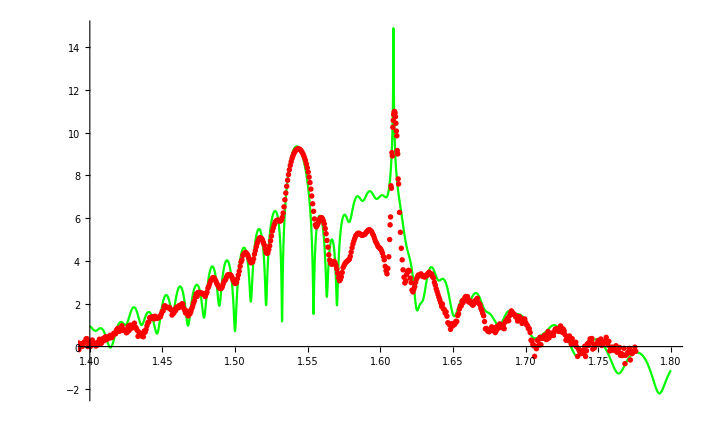

```mathematica
(*model=rSpec[q,polFactor,eRad,layerNum=3,rho,dSpace,formFactor,mDefaults,nBarDefaults,{delSrTiO3Fit,delSrRuO3Fit,delBiFeO3Fit,delCoFit}];*)
loggedData=MapAt[Log,fitData,{All,2}];
loggedModel=Log[rSpec[q,polFactor,eRad,layerNum=3,rho,dSpace,formFactor,mDefaults,nBarDefaults,{delSTOFit,delSrRuO3Fit,delBiFeO3Fit,delCoFit}]];
fit=FindFit[loggedData,{loggedModel,{delMin<delSTOFit<delMax,delMin<delSrRuO3Fit<delMax,delMin<delBiFeO3Fit<delMax,delMin<delCoFit<delMax}},
{{delSTOFit,delDefaults[[1]]},{ delSrRuO3Fit,delDefaults[[2]]},{delBiFeO3Fit, delDefaults[[3]]}, {delCoFit,delDefaults[[4]]}},q,Method->"NMinimize"]
Show[{Plot[Evaluate[loggedModel/.fit],{q,1.4,1.8},PlotStyle->Green],ListPlot[loggedData,PlotStyle->Red]}]
```